```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jmac/Nutstore Files/1Project/1Qdia/code/Git/Fig3/Nq1_block1_rhov1/Res

```mathematica
lossP = Import["lossPv0.txt","Data"];
```

```mathematica
lossRes=lossP⟦All,{2,4}⟧;
PsqureRes = lossP⟦All,{2,6}⟧;
PurityRes = lossP⟦All,{2,8}⟧;
offDRes= lossP⟦All,{2,10}⟧;
```

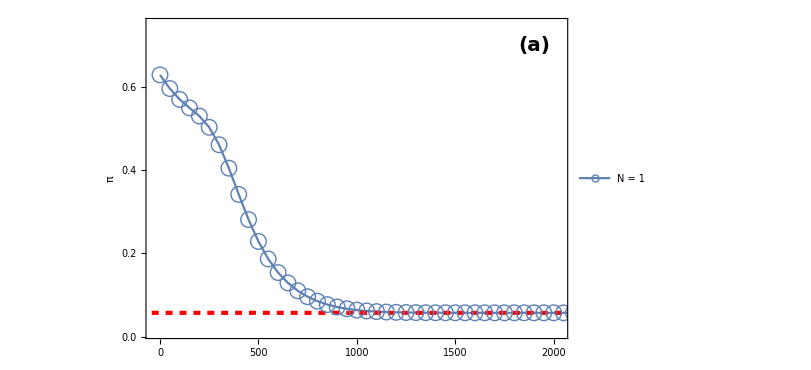

```mathematica
Figa=ListLinePlot[lossRes,PlotRange->{{-30,2030},{0.01,0.75}},FrameLabel->{Style["",Black,Directive[Large],FontSize->20],Style["π",(*Italic,*)Directive[Large],Black,FontSize->20]},RotateLabel->False,
GridLines->{{},{0.057}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->Style["○",FontSize->16],
FrameTicks->{{{{0,"0.0"},0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,{1.0,"1.0"}},None},{{0,500,1000,1500,2000},None}},
PlotLegends->Placed[{Style[" N = 1 ",Bold,FontSize->14]},{0.78,0.44}],Epilog->Inset[Style["(a)",Bold,FontSize->20],{1900,0.70}],
ImageSize->{600,291},ImagePadding->{{80,80},{1,10}}]
```

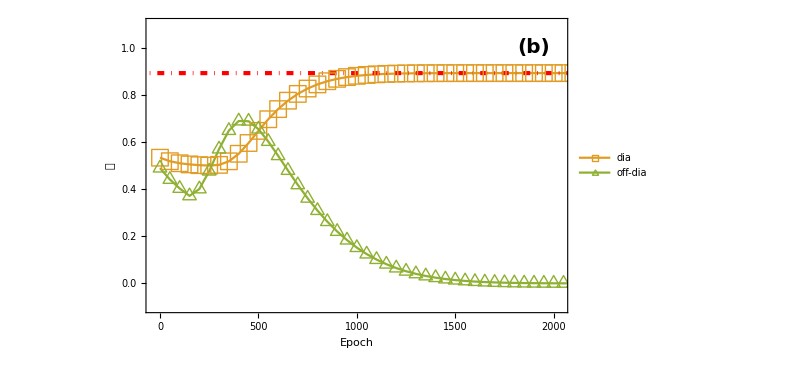

```mathematica
Figb=ListLinePlot[{lossRes+100,PsqureRes,offDRes},PlotRange->{{-30,2030},{-0.1,1.1}},FrameLabel->{{Style["𝒟",Italic,Directive[Large],Black,FontSize->20],Style["(|ρ_(('_(off-dia))_)|)^(—————–)",Italic,Directive[Large],Black,FontSize->20]},{Style["Epoch",Black,Directive[Large],FontSize->20],None}},RotateLabel->True,
GridLines->{{},{PurityRes⟦1,2⟧}},GridLinesStyle->Directive[Red,DotDashed,Thickness[0.005]],
Frame->True,Axes->None,FrameStyle->Thick,FrameTicksStyle->Directive[Black,Bold,16],PlotMarkers->{Style["○",FontSize->16],Style["□",FontSize->17],Style["△",FontSize->16]},
FrameTicks->{{{{0,"0.0"},0.2,0.4,0.6,0.8,{1.0,"1.0"}},{{0,"0.0"},0.2,0.4,0.6,0.8,{1.0,"1.0"}}},{{0,500,1000,1500,2000},None}},
PlotLegends->Placed[{None,Style["dia",Bold,FontSize->14],Style["off-dia",Bold,FontSize->14]},{0.78,0.44}],Epilog->Inset[Style["(b)",Bold,FontSize->20],{1900,1.0}],
ImageSize->{600,340},ImagePadding->{{80,80},{60,0}}]
```

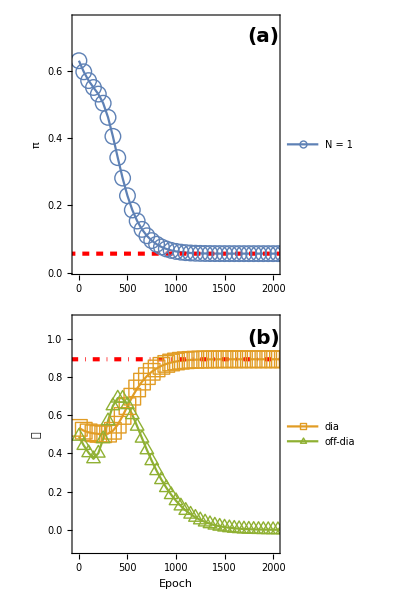

```mathematica
Fig3=Grid[{{Figa},{Figb}},Spacings->{Automatic, -0.8}]
```

```mathematica
Export["./Fig3N1v.pdf",Fig3]
```

./Fig3N1v.pdf